```mathematica
f[x_,y_]:=Sqrt[1/( π)]*(Exp[-(x-2)^2]*Exp[-(y+2)^2]+Exp[-(y-2)^2]*Exp[-(x+2)^2])
```

```mathematica
NIntegrate[f[x,y]^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

1.

```mathematica
Plot3D[f[x,y]^2,{x,-4,4},{y,-4,4}, PlotRange -> {0,0.5}]
```

-Graphics3D-

```mathematica
_□
```

```mathematica
fs[x_,y_]:=Evaluate[Integrate[f[x,y]^2,{x,-Infinity,Infinity}]*Integrate[f[x,y]^2,{y,-Infinity,Infinity}]]
```

```mathematica
NIntegrate[fs[x,y],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

```mathematica
1.0000002406664648+
```

```mathematica
e[x_,y_]:=Evaluate[f[x,y]^2-fs[x,y]]
```

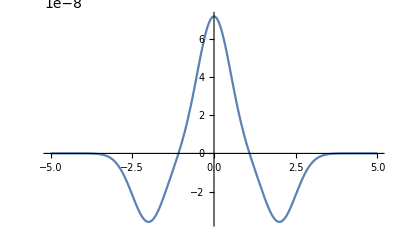

```mathematica
Plot[e[x,0],{x,-5,5}]
```

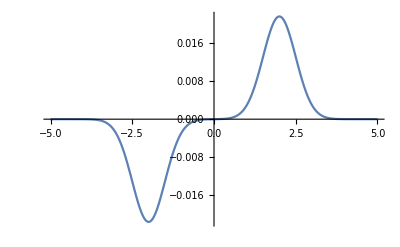

```mathematica
Plot[e[x,-1],{x,-5,5}]
```

```mathematica
NIntegrate[Abs[e[x,y]],{x,-Infinity,Infinity},{y,-Infinity,Infinity},WorkingPrecision->12]
```

0.999873704747

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.896581

```mathematica
N[%24]
```

0.0740147